## The Stoplight Problem

You have a 1-liter bucket into which you mix in 3 kinds of paint -- red, yellow, and green. Each paint color can be of any volume between 0 and 1 liter and all three colors must add up to 1 liter. The stoplight problem asks: What is the color of the bucket as a whole (and the choices are red, yellow, or green) based on the proportions of red, yellow, and green in the bucket?
Of course the paint mixture in the bucket will usually be far from one of the original colors, but the task is to determine which one of our original colors it best represents. 
The stoplight problem gets its name from the stoplights on dashboards -- the color of these stoplights at a higher level depend on the colors of component stoplights at a lower level. Each of the component stoplights (red, yellow, or green) is weighted between 0 and 1 and the all the component weights add up to 1. The question then is: What is the color of the higher level stoplight based on the colors of the component stoplights?

## Risk Aversion

The idea of a dashboard is to give the user an appropriate level of warning; it’s better to err on the side of reporting a worse outcome just to keep users appropriately warned. Even if only 40% of the paint in the bucket is red, we might want to signal that the bucket color is red in order to give the user early warning of an impending problem.
The relative risk of a red versus a yellow versus a green is modeled by giving each color a certain number of points that capture the relative difference between their risk levels. This is itself a weighting system. 
Let’s set the relative weights as follows:

```mathematica
rRisk = 100;
yRisk = 75;
gRisk = 25;
```

This shows that the risk aversion to red (rRisk) is 4 times greater than the risk aversion to green (gRisk). The risk aversion to yellow (yRisk) is 3 times greater than the risk aversion to green. And finally, the risk aversion to red is 33% greater than the risk aversion to yellow.

## Generating the Trials

We need a bunch of 3-tuples. Each 3-tuple stands for a certain mix of volumes of red, yellow, and green in our bucket. The individual volumes should always add up to 1; hence the values of each 3-tuple must sum to 1.
Let’s simulate n 3-tuples.

We set the number of trials we want.

```mathematica
n = 10000;
```

```mathematica
reds = RandomReal[1,n];
```

```mathematica
yellows = RandomReal[1,n];
```

Put the reds and yellows together and keep the ones that add up to less than 1.

```mathematica
tot = reds + yellows;
```

The positions of the reds and yellows we keep are as follows:

```mathematica
keep = Flatten[Position[tot /. x_ /; x≤ 1 -> "ok","ok"]];
```

```mathematica
greens = 1-tot;
```

Create the data set

```mathematica
d = {reds[[#]],yellows[[#]],greens[[#]]} & /@ keep;
```

## Validating the Model

Let’s check the size and the distribution of red, yellow, and green values to be sure that the simulation is appropriate. When we hold a color value fixed, e.g. at 0.5, we want the other color values to be well distributed so that we can be confident that the values of the 3-tuples are well “mixed” so we’re able to simulate most possible outcomes.

```mathematica
Length[d]
```

4978

How many reds are greater than 0.5?

```mathematica
r5l = Length[Select[d, #[[1]] ≥ 0.5 &]]
```

1269

Get the set of trials where the reds are greater than 0.5

```mathematica
r5 = Select[d,#[[1]] ≥ 0.5 &];
```

How are the reds greater than 0.5 distributed?

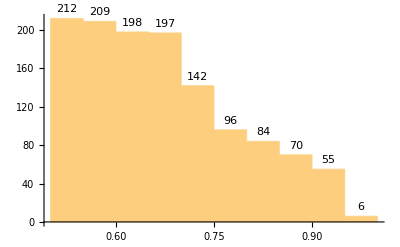

```mathematica
r5reds = Histogram[r5[[All,1]], LabelingFunction->Above]
```

How does this compare with the distribution of reds in general across the data set?

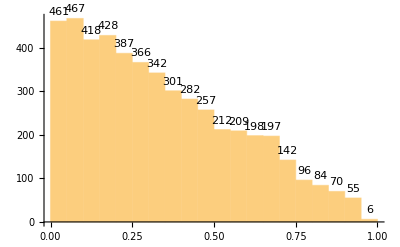

```mathematica
dreds = Histogram[d[[All,1]], LabelingFunction->Above]
```

We learn that this random method of generating 3-tuples that add to 1 doesn’t generate values for the colors that are uniformly distributed. That makes sense because as one color “grows” there are fewer and fewer acceptable values the other colors can take to satisfy the fact they must total to 1.
We can see this with a simultaneous histogram of all three color distributions in our data set.

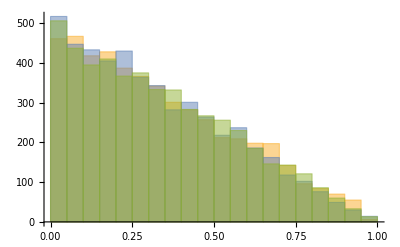

```mathematica
ddist = Histogram[{d[[All,1]], d[[All,2]], d[[All,3]]}]
```

There are relatively few cases of values at the extreme end of the scale. But this is OK, because the extreme cases are easy -- if the paint in the bucket is entirely red, then the color of the bucket should be red without question. It’s the middle range values that we need to worry about.

When reds are greater than 0.5, how are the yellows and greens distributed?

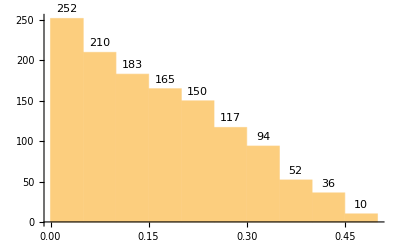

```mathematica
r5greens = Histogram[r5[[All,2]], LabelingFunction->Above]
```

We can see immediately that when red is greater than 0.5, there are very few greens near 0.5. And similarly for yellows.

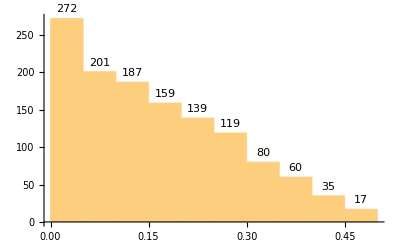

```mathematica
r5yellows = Histogram[r5[[All,3]], LabelingFunction->Above]
```

## Calculating Risk-Adjusted Total Scores

For each of the 3-tuples in the data set we calculate a total score based on the relative differences between reds, yellows, and greens.

```mathematica
s = Round[rRisk*#[[1]] + yRisk*#[[2]] + gRisk*#[[3]]] &/@ d;
```

Check to see if this gives the right results:

```mathematica
Take[s,5]
```

{84,44,79,43,65}

Now append the scores to the 3-tuples to form a set of 4-tuples consisting of the red, yellow, and green values and the resulting score.

```mathematica
ds = Flatten[#] & /@ Transpose[{d,s}];
```

Check if this gives the right results:

```mathematica
Take[ds,5]
```

{{0.599008,0.286888,0.114104,84},{0.155456,0.154406,0.690138,44},{0.722352,0.000816263,0.276832,79},{0.112006,0.18202,0.705974,43},{0.0231574,0.756015,0.220828,65}}

It seems OK. The next step is to see what kinds of segmentation emerge. These will point us to break points we can use to determine the color of the entire bucket based on the mix of colors in the bucket.

## Segmentation of Scores by Color Weight

Let’s look at the way in which the scores fall as the mix of reds grows from 0.1 to 1 in increments of 0.1. This should give us a sense of how the break points emerge.

Here is the distribution of scores for red less than or equal to 0.1, 0.2, ..., 1 in weight.

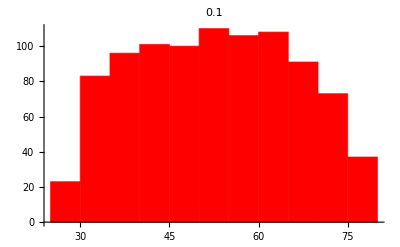
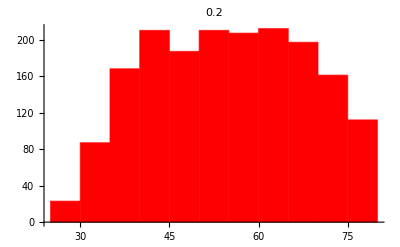
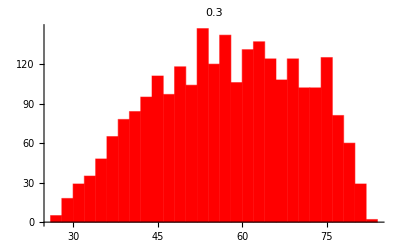
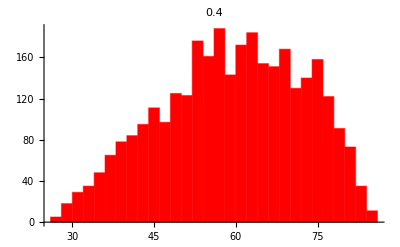
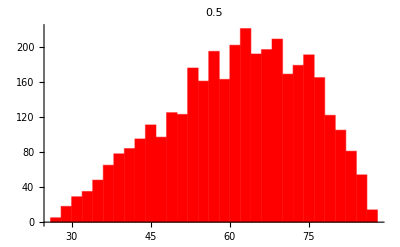
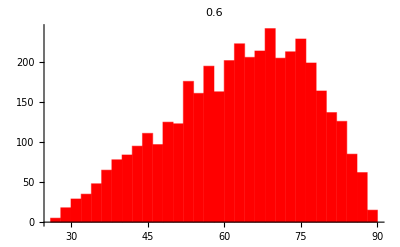
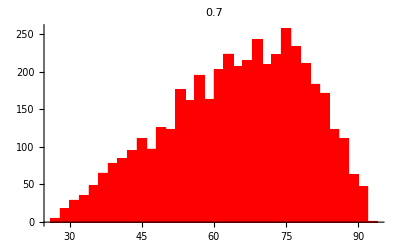
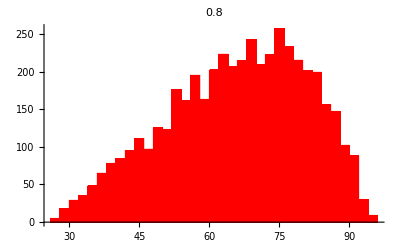

```mathematica
rsegs = Table[Select[ds, #[[1]] ≤ i &], {i,0.1,1,0.1}];
rsdist = Table[Histogram[rsegs[[i]][[All,4]], PlotLabel-> N[i/10], ChartStyle-> Red], {i,1,Length[rsegs]}]
```

Even when red is less than or equal to 0.1 in weight, the scores can get to as high as the 60s. So we know that when we see these kinds of scores, the overall stoplight can’t be red -- it has to be yellow or green. But which one? That would depend on the score distributions for the yellows and greens which we can get to next.

These are for the yellows:

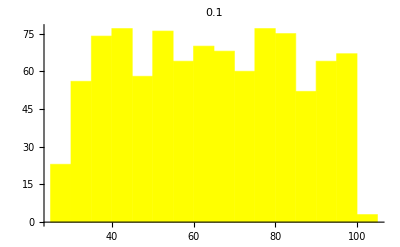
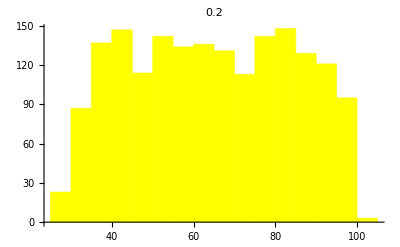
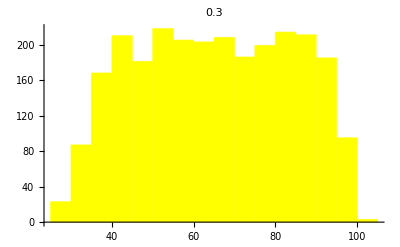
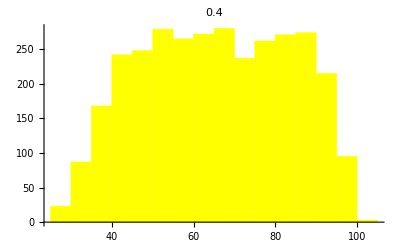
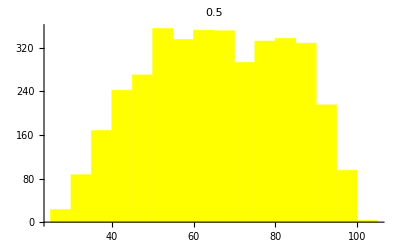
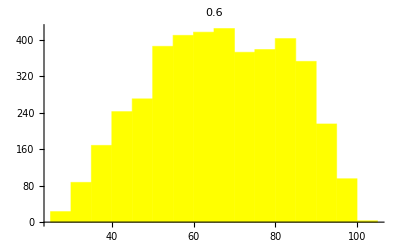
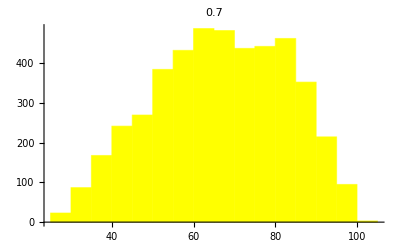
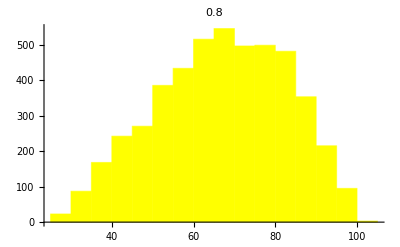

```mathematica
ysegs = Table[Select[ds, #[[2]] ≤ i &], {i,0.1,1,0.1}];
ysdist = Table[Histogram[ysegs[[i]][[All,4]],PlotLabel-> N[i/10], ChartStyle-> Yellow], {i,1,Length[ysegs]}]
```

And these are for the greens:

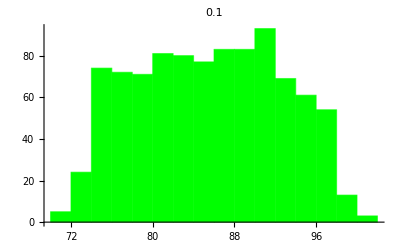
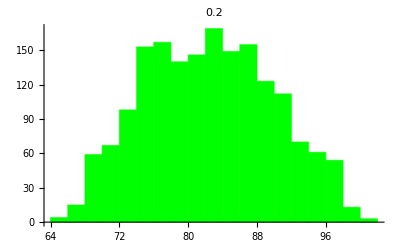
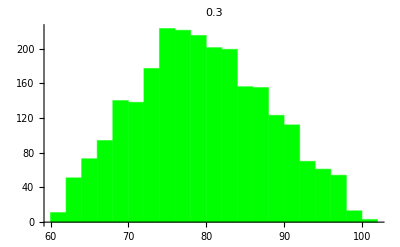
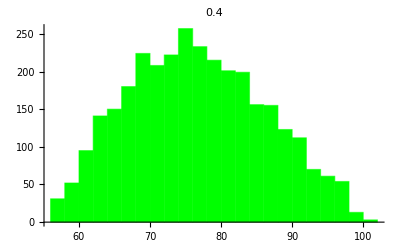
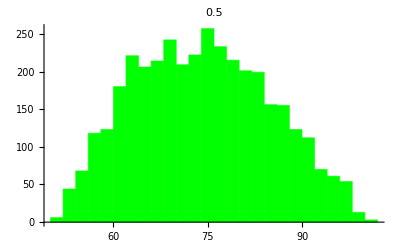
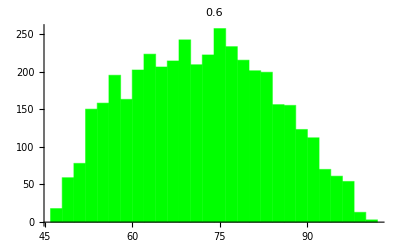
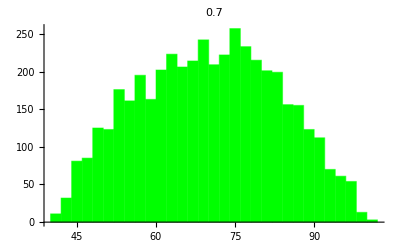
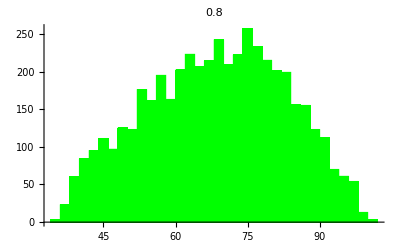

```mathematica
gsegs = Table[Select[ds, #[[3]] ≤ i &], {i,0.1,1,0.1}];
gsdist = Table[Histogram[gsegs[[i]][[All,4]],PlotLabel-> N[i/10], ChartStyle-> Green], {i,1,Length[gsegs]}]
```

## Segmentation of Color Weights by Score

A better way to arrive at the overall stoplight coloring scheme is by flipping what we did above; instead of looking at the weights and then asking what the scores can be for those weights, we flip around and ask for a given score, what is the distribution of red, yellow, and green weights. This will help us better detect the weird edge cases.

Here are the distributions of red, yellow, and green weights for scores under 40.

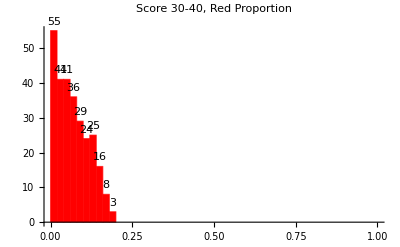

```mathematica
scoresegs40 = Select[ds, #[[4]]< 40 &];
rssdist40 = Histogram[scoresegs40[[All,1]], LabelingFunction -> Above, PlotLabel->"Score 30-40, Red Proportion", ChartStyle->Red, PlotRange-> {{0,1}, Automatic}]
```

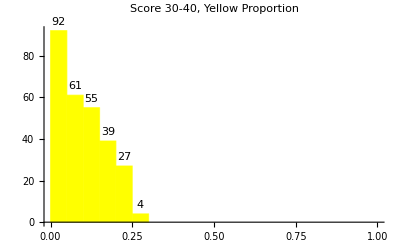

```mathematica
yssdist40 = Histogram[scoresegs40[[All,2]], PlotLabel->"Score 30-40, Yellow Proportion", LabelingFunction -> Above, ChartStyle->Yellow, PlotRange-> {{0,1}, Automatic}]
```

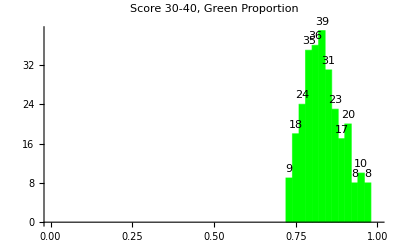

```mathematica
gssdist40 = Histogram[scoresegs40[[All,3]], PlotLabel->"Score 30-40, Green Proportion", LabelingFunction -> Above, ChartStyle->Green, PlotRange-> {{0,1}, Automatic}]
```

Clearly, when the score is under 40, the stoplight should be GREEN.

Let’s do the same for scores between 40 and 50.

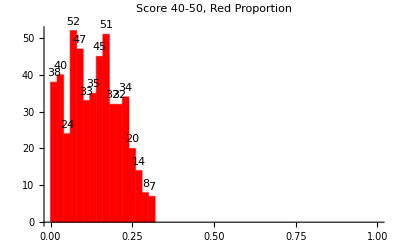

```mathematica
scoresegs50 = Select[ds, #[[4]] ≥ 40 && #[[4]]< 50 &];
rssdist50 = Histogram[scoresegs50[[All,1]], PlotLabel->"Score 40-50, Red Proportion", LabelingFunction -> Above, ChartStyle -> Red, PlotRange-> {{0,1}, Automatic}]
```

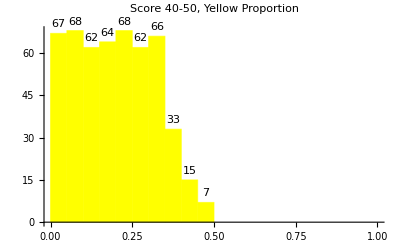

```mathematica
yssdist50 = Histogram[scoresegs50[[All,2]], PlotLabel->"Score 40-50, Yellow Proportion", LabelingFunction -> Above, ChartStyle-> Yellow, PlotRange-> {{0,1}, Automatic}]
```

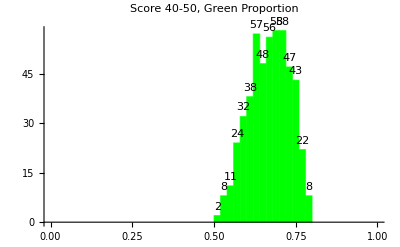

```mathematica
gssdist50= Histogram[scoresegs50[[All,3]], PlotLabel->"Score 40-50, Green Proportion", LabelingFunction -> Above, ChartStyle -> Green, PlotRange-> {{0,1}, Automatic}]
```

Looks like the stoplight color should be GREEN for this range too.

Let’s check for the range from 50 to 60.

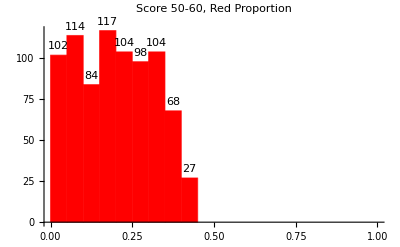

```mathematica
scoresegs60 = Select[ds, #[[4]] ≥ 50 && #[[4]]< 60 &];
rssdist60 = Histogram[scoresegs60[[All,1]], PlotLabel->"Score 50-60, Red Proportion", LabelingFunction -> Above, ChartStyle->Red, PlotRange-> {{0,1}, Automatic}]
```

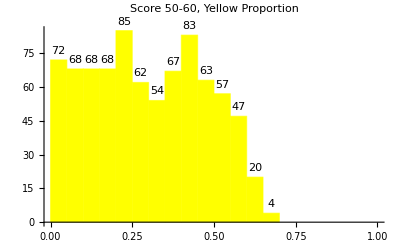

```mathematica
yssdist60 = Histogram[scoresegs60[[All,2]], PlotLabel->"Score 50-60, Yellow Proportion", LabelingFunction -> Above, ChartStyle->Yellow, PlotRange-> {{0,1}, Automatic}]
```

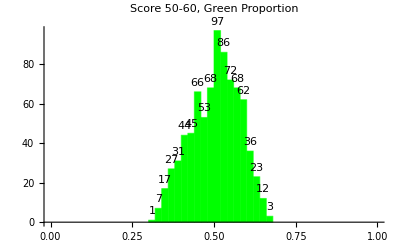

```mathematica
gssdist60= Histogram[scoresegs60[[All,3]], PlotLabel->"Score 50-60, Green Proportion", LabelingFunction -> Above, ChartStyle->Green, PlotRange-> {{0,1}, Automatic}]
```

The reds can still get up to 0.3, but the yellows now range all the way to 0.8. This range is clearly a YELLOW.

Let’s check the range from 60 to 70.

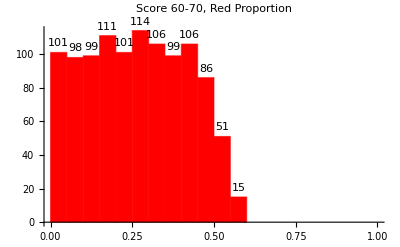

```mathematica
scoresegs70 = Select[ds, #[[4]] ≥ 60 && #[[4]]< 70 &];
rssdist70 = Histogram[scoresegs70[[All,1]], PlotLabel->"Score 60-70, Red Proportion", LabelingFunction -> Above, ChartStyle->Red, PlotRange-> {{0,1}, Automatic}]
```

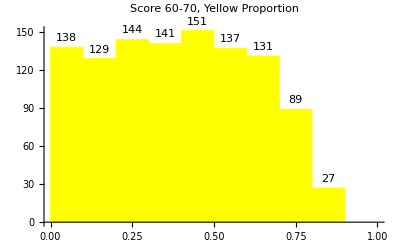

```mathematica
yssdist70 = Histogram[scoresegs70[[All,2]], PlotLabel->"Score 60-70, Yellow Proportion", LabelingFunction -> Above, ChartStyle->Yellow, PlotRange-> {{0,1}, Automatic}]
```

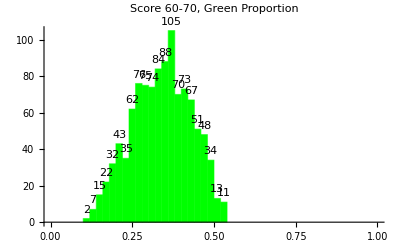

```mathematica
gssdist70= Histogram[scoresegs70[[All,3]], PlotLabel->"Score 60-70, Green Proportion", LabelingFunction -> Above, ChartStyle->Green, PlotRange-> {{0,1}, Automatic}]
```

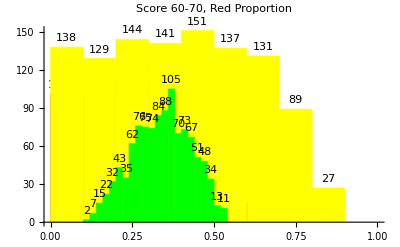

```mathematica
Show[rssdist70,yssdist70,gssdist70]
```

Still looks like YELLOW.

Let’s check for the range from 70 to 80.

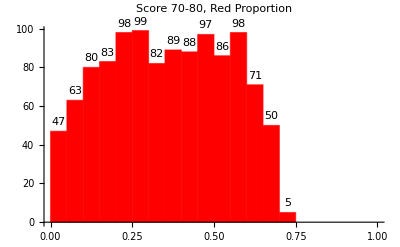

```mathematica
scoresegs80 = Select[ds, #[[4]] ≥ 70 && #[[4]]< 80 &];
rssdist80 = Histogram[scoresegs80[[All,1]], PlotLabel->"Score 70-80, Red Proportion", LabelingFunction -> Above, PlotRange-> {{0,1}, Automatic}, ChartStyle-> Red]
```

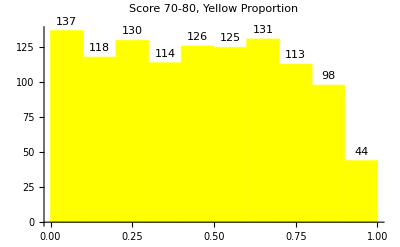

```mathematica
yssdist80 = Histogram[scoresegs80[[All,2]], PlotLabel->"Score 70-80, Yellow Proportion", LabelingFunction -> Above, PlotRange-> {{0,1}, Automatic}, ChartStyle->Yellow]
```

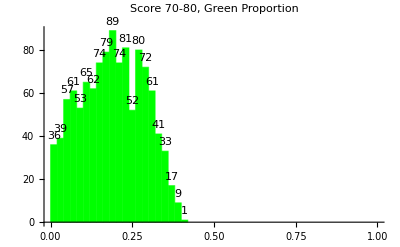

```mathematica
gssdist80= Histogram[scoresegs80[[All,3]], PlotLabel->"Score 70-80, Green Proportion", LabelingFunction -> Above, PlotRange-> {{0,1}, Automatic}, ChartStyle->Green]
```

The reds are beginning to grow, but the yellows still have it -- the range between 70 and 80 is still YELLOW.

Let’s check for values at and above 80.

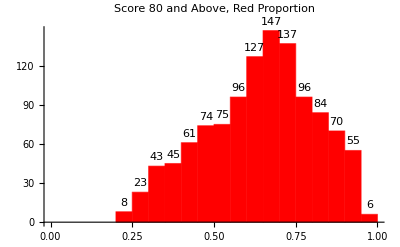

```mathematica
scoresegsAbove80 = Select[ds, #[[4]] ≥ 80 &];
rssdistAbove80 = Histogram[scoresegsAbove80[[All,1]], PlotLabel->"Score 80 and Above, Red Proportion", LabelingFunction -> Above, PlotRange-> {{0,1}, Automatic}, ChartStyle->Red]
```

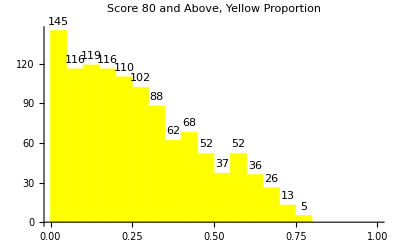

```mathematica
yssdistAbove80 = Histogram[scoresegsAbove80[[All,2]], PlotLabel->"Score 80 and Above, Yellow Proportion", LabelingFunction -> Above, PlotRange-> {{0,1}, Automatic}, ChartStyle->Yellow]
```

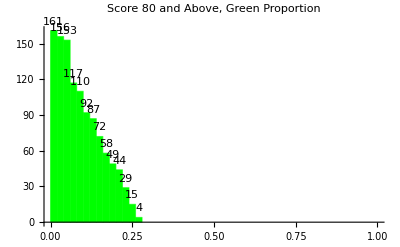

```mathematica
gssdistAbove80= Histogram[scoresegsAbove80[[All,3]], PlotLabel->"Score 80 and Above, Green Proportion", LabelingFunction -> Above, PlotRange-> {{0,1}, Automatic}, ChartStyle->Green]
```

Clearly RED is the overall stoplight color for scores above 80.

## Results

We set up some risk aversion weights and calculated scores based on those weights after checking the segmentation of scores. When the risk aversion weights are changed, the segments will be different.

The first set of risk aversion values we set up were Red = 100, Yellow = 60, and Green = 30. This makes Yellow two thirds as risky as a Red and a Green one third as risky as a red.

```mathematica
riskMetrics1 = {"Risk Aversion Metrics",{"Risk of Red","Risk of Yellow", "Risk of Green"},{100, 60, 30}};
stoplightColors1 = {"Overall Stoplight Color",  "GREEN - less than 50", "YELLOW - from 50 to 70", "RED - over 70"};
results1 = {riskMetrics1, stoplightColors1}
```

{{Risk Aversion Metrics,{Risk of Red,Risk of Yellow,Risk of Green},{100,60,30}},{Overall Stoplight Color,GREEN - less than 50,YELLOW - from 50 to 70,RED - over 70}}

With this first set of risk aversion values, scores less than 50 are GREEN, scores from 50 to 70 are YELLOW, and scores above 70 are RED.
We then used a second set of risk aversion values: Red = 100, Yellow = 75, Green = 25. Under this set of metrics, Red and Yellow are closer together in risk and the risk of Green is further reduced.

```mathematica
riskMetrics2 = {"Risk Aversion Metrics",{"Risk of Red","Risk of Yellow", "Risk of Green"},{100, 75, 25}};
stoplightColors2 = {"Overall Stoplight Color",  "GREEN - less than 50", "YELLOW - from 50 to 80", "RED - over 80"};
results2 = {riskMetrics2, stoplightColors2}
```

{{Risk Aversion Metrics,{Risk of Red,Risk of Yellow,Risk of Green},{100,75,25}},{Overall Stoplight Color,GREEN - less than 50,YELLOW - from 50 to 80,RED - over 80}}

With this second set of risk aversion values, scores less than 50 are GREEN (as before), scores between 50 and 80 are now YELLOW, and scores above 80 are RED. The range of scores for which the overall stoplight is YELLOW increases under the second set of risk aversion metrics. This is the set that we will use for the dashboard calculations.

## Validating the Scheme

To validate the scheme we’ve come up with for the overall stoplight color, let’s check the edge cases. 
What is the behavior of the color mixture around the break point for GREEN? In other words, what kinds of red, yellow, green scores do we see when the overall score is between 45 and 55?

For these values, isolate in particular yellow scores that are within 0.1 (positive or negative) of the green score.

In the list below, the values are {red weight, yellow weight, green weight, score}.

```mathematica
vg = Sort[Select[Select[ds, #[[4]] > 45 && #[[4]] ≤ 55 &], Abs[#[[3]]-#[[2]]] ≤ 0.1 &], #1[[4]] < #2[[4]] &]
```

{{0.00231285,0.460157,0.53753,48},{0.014287,0.444335,0.541378,48},{0.0109828,0.455322,0.533695,49},{0.0278853,0.447173,0.524942,49},{0.00439886,0.475206,0.520395,49},{0.00536841,0.47986,0.514772,49},{0.00896123,0.476464,0.514575,49},{0.00791532,0.459807,0.532278,49},{0.0222383,0.455551,0.52221,49},{0.0253994,0.438927,0.535674,49},{0.0257606,0.455617,0.518622,50},{0.0246318,0.467923,0.507445,50},{0.0189978,0.468765,0.512238,50},{0.0314685,0.453016,0.515515,50},{0.039447,0.438319,0.522234,50},{0.00440897,0.499123,0.496468,50},{0.0183696,0.465379,0.516251,50},{0.0143177,0.468922,0.51676,50},{0.0185268,0.463296,0.518177,50},{0.0364842,0.44148,0.522035,50},{0.00833982,0.492241,0.49942,50},{0.0168868,0.482035,0.501079,50},{0.0203001,0.494813,0.484887,51},{0.00093343,0.514291,0.484776,51},{0.0372619,0.454557,0.508181,51},{0.0680375,0.419557,0.512405,51},{0.0663291,0.425949,0.507722,51},{0.0247944,0.488723,0.486482,51},{0.0402661,0.450425,0.509309,51},{0.0558664,0.428211,0.515923,51},{0.0429733,0.4563,0.500726,51},{0.0322898,0.473783,0.493927,51},{0.0475454,0.469359,0.483095,52},{0.0733481,0.43178,0.494872,52},{0.0143767,0.526334,0.459289,52},{0.0770645,0.433175,0.48976,52},{0.00662983,0.53906,0.45431,52},{0.0886035,0.407373,0.504023,52},{0.0669769,0.441049,0.491974,52},{0.0661353,0.449603,0.484262,52},{0.0571584,0.457735,0.485106,52},{0.00543796,0.538514,0.456048,52},{0.0480811,0.461292,0.490626,52},{0.0707321,0.443273,0.485995,52},{0.0877582,0.406836,0.505406,52},{0.00366887,0.53558,0.460751,52},{0.0639666,0.440201,0.495832,52},{0.0546689,0.452342,0.492989,52},{0.0553607,0.458039,0.4866,52},{0.0265283,0.491021,0.482451,52},{0.0746615,0.424554,0.500785,52},{0.0586105,0.446172,0.495218,52},{0.0372378,0.494055,0.468707,52},{0.0824274,0.416667,0.500906,52},{0.0789147,0.427499,0.493587,52},{0.110571,0.402343,0.487087,53},{0.0861013,0.433268,0.480631,53},{0.0829392,0.441235,0.475826,53},{0.0647141,0.470723,0.464563,53},{0.0137517,0.531053,0.455195,53},{0.0222149,0.524603,0.453182,53},{0.0444965,0.494059,0.461445,53},{0.0689612,0.45445,0.476589,53},{0.104626,0.407989,0.487385,53},{0.0910051,0.415291,0.493703,53},{0.0949524,0.412589,0.492458,53},{0.0202674,0.526683,0.453049,53},{0.0204746,0.53618,0.443345,53},{0.0785083,0.451154,0.470338,53},{0.0508636,0.490852,0.458284,53},{0.0525517,0.48173,0.465718,53},{0.0921624,0.414008,0.493829,53},{0.0201647,0.533487,0.446348,53},{0.0998061,0.419822,0.480372,53},{0.0265019,0.515445,0.458053,53},{0.0585132,0.481826,0.459661,53},{0.0323504,0.504481,0.463168,53},{0.0543225,0.50318,0.442497,54},{0.0478019,0.504913,0.447285,54},{0.0264252,0.530703,0.442872,54},{0.106117,0.419755,0.474128,54},{0.119266,0.401777,0.478958,54},{0.092838,0.441192,0.46597,54},{0.0986848,0.437216,0.464099,54},{0.10418,0.429749,0.466071,54},{0.0277329,0.528948,0.443319,54},{0.0961363,0.437759,0.466105,54},{0.0556453,0.500091,0.444264,54},{0.11199,0.415448,0.472563,54},{0.110449,0.410392,0.479159,54},{0.114873,0.416816,0.468311,54},{0.0917926,0.450771,0.457437,54},{0.0455396,0.503223,0.451238,54},{0.0374677,0.523243,0.439289,54},{0.0471909,0.513619,0.43919,54},{0.0794548,0.460606,0.45994,54},{0.0840268,0.457217,0.458757,54},{0.110919,0.411682,0.477399,54},{0.0266312,0.533863,0.439506,54},{0.0500225,0.51455,0.435427,54},{0.088715,0.459073,0.452212,55},{0.116945,0.430739,0.452316,55},{0.0945691,0.453025,0.452406,55},{0.0934147,0.468588,0.437997,55},{0.0651572,0.510362,0.424481,55},{0.146431,0.389613,0.463955,55},{0.104508,0.448653,0.446839,55},{0.13519,0.397686,0.467124,55},{0.11228,0.431373,0.456347,55},{0.0590579,0.512085,0.428857,55},{0.117019,0.414732,0.468248,55},{0.118666,0.418744,0.46259,55},{0.0892336,0.458235,0.452532,55},{0.090317,0.46118,0.448503,55},{0.0548945,0.521825,0.42328,55},{0.115477,0.432002,0.452521,55},{0.13672,0.399816,0.463464,55},{0.0657588,0.498452,0.43579,55}}

There are obviously a lot of edge cases. We can handle them by first flagging these and then perhaps indicating them with an “inbetween” color (e.g. something inbetween GREEN and YELLOW).

Finally, let’s look at the border between YELLOW and RED. We look at scores from 75 to 85 and look for the absolute difference between red and yellow weights to be less than or equal to 0.1.

```mathematica
vy = Sort[Select[Select[ds, #[[4]] > 75 && #[[4]] ≤ 85 &], Abs[#[[1]]-#[[2]]] ≤ 0.1 &], #1[[4]] < #2[[4]] &]
```

{{0.413129,0.402565,0.184306,76},{0.390946,0.426921,0.182133,76},{0.401867,0.410748,0.187385,76},{0.42126,0.381331,0.19741,76},{0.373705,0.451507,0.174788,76},{0.407086,0.404734,0.188179,76},{0.365108,0.464001,0.170891,76},{0.443693,0.353996,0.202311,76},{0.378481,0.443579,0.17794,76},{0.440722,0.359426,0.199852,76},{0.428535,0.385118,0.186347,76},{0.379359,0.448981,0.17166,76},{0.410894,0.41329,0.175815,76},{0.430813,0.374316,0.194871,76},{0.367705,0.459731,0.172563,76},{0.418531,0.396568,0.1849,76},{0.38898,0.42852,0.1825,76},{0.422506,0.400512,0.176983,77},{0.397733,0.450988,0.151279,77},{0.440148,0.377492,0.18236,77},{0.447669,0.367474,0.184857,77},{0.400847,0.447941,0.151212,77},{0.400365,0.443608,0.156027,77},{0.38218,0.469912,0.147907,77},{0.418822,0.421075,0.160102,77},{0.383777,0.470899,0.145324,77},{0.428725,0.402336,0.168939,77},{0.394555,0.448168,0.157276,77},{0.423651,0.396849,0.1795,77},{0.375319,0.469282,0.155399,77},{0.406794,0.430249,0.162957,77},{0.378765,0.465058,0.156177,77},{0.418281,0.408183,0.173537,77},{0.440691,0.379045,0.180265,77},{0.416751,0.405545,0.177703,77},{0.415713,0.406472,0.177815,77},{0.433782,0.397311,0.168906,77},{0.439809,0.384736,0.175455,77},{0.398625,0.432243,0.169132,77},{0.436216,0.384856,0.178928,77},{0.426707,0.410032,0.163261,78},{0.421098,0.419509,0.159393,78},{0.428296,0.426458,0.145246,78},{0.395359,0.469933,0.134708,78},{0.393577,0.471529,0.134894,78},{0.431752,0.409957,0.158291,78},{0.450318,0.392264,0.157418,78},{0.424066,0.428059,0.147875,78},{0.451061,0.375935,0.173004,78},{0.449528,0.390922,0.15955,78},{0.443281,0.385218,0.171501,78},{0.467503,0.379436,0.153061,79},{0.392838,0.488625,0.118537,79},{0.406861,0.460854,0.132285,79},{0.398667,0.488479,0.112854,79},{0.447574,0.404571,0.147855,79},{0.446665,0.402461,0.150874,79},{0.400393,0.474199,0.125408,79},{0.396616,0.487881,0.115502,79},{0.452964,0.403292,0.143744,79},{0.435741,0.429953,0.134306,79},{0.39506,0.491655,0.113286,79},{0.469719,0.401876,0.128405,80},{0.446681,0.421038,0.132281,80},{0.454799,0.417176,0.128025,80},{0.430652,0.448813,0.120535,80},{0.420161,0.475325,0.104514,80},{0.472292,0.397816,0.129891,80},{0.45734,0.415899,0.126761,80},{0.467475,0.404781,0.127744,80},{0.464585,0.398929,0.136486,80},{0.427731,0.467551,0.104718,80},{0.455529,0.4094,0.13507,80},{0.455301,0.423963,0.120737,80},{0.461457,0.417966,0.120577,81},{0.415545,0.486836,0.0976184,81},{0.474404,0.410858,0.114738,81},{0.422065,0.490542,0.0873922,81},{0.472363,0.418492,0.109146,81},{0.416547,0.490989,0.0924638,81},{0.485113,0.393458,0.121428,81},{0.42766,0.481602,0.0907379,81},{0.480815,0.407519,0.111666,81},{0.427703,0.486286,0.0860111,81},{0.415441,0.499969,0.0845898,81},{0.459542,0.43875,0.101707,81},{0.419037,0.484716,0.0962466,81},{0.416156,0.504741,0.0791025,81},{0.41445,0.488454,0.0970963,81},{0.459288,0.445509,0.0952027,82},{0.431366,0.49639,0.0722437,82},{0.45532,0.448125,0.0965545,82},{0.429124,0.489911,0.0809651,82},{0.490968,0.398147,0.110885,82},{0.467854,0.439463,0.0926829,82},{0.469245,0.426507,0.104248,82},{0.422042,0.513922,0.0640359,82},{0.469326,0.43304,0.0976343,82},{0.454972,0.45255,0.0924774,82},{0.473765,0.421416,0.104819,82},{0.442415,0.477634,0.0799513,82},{0.481681,0.423026,0.0952923,82},{0.460775,0.440991,0.0982344,82},{0.470528,0.426904,0.102568,82},{0.447619,0.477547,0.0748339,82},{0.448405,0.464605,0.0869899,82},{0.41565,0.507595,0.0767551,82},{0.435693,0.488433,0.0758742,82},{0.451102,0.480482,0.0684163,83},{0.488354,0.433128,0.078518,83},{0.464432,0.468946,0.0666217,83},{0.428964,0.516811,0.0542241,83},{0.452965,0.471876,0.0751595,83},{0.465676,0.458121,0.076203,83},{0.473068,0.45456,0.0723719,83},{0.427925,0.510278,0.0617974,83},{0.498364,0.413174,0.0884623,83},{0.443772,0.497758,0.0584696,83},{0.489413,0.428613,0.0819743,83},{0.491846,0.428844,0.0793099,83},{0.480478,0.43869,0.0808314,83},{0.494062,0.40998,0.0959579,83},{0.505151,0.407133,0.0877157,83},{0.458857,0.46597,0.0751731,83},{0.453527,0.489487,0.0569862,83},{0.480603,0.44502,0.0743763,83},{0.499831,0.414832,0.085337,83},{0.454535,0.479498,0.0659667,83},{0.460515,0.489797,0.0496875,84},{0.445921,0.512024,0.0420547,84},{0.444763,0.504546,0.050691,84},{0.452976,0.493402,0.0536221,84},{0.493977,0.445499,0.0605239,84},{0.473698,0.462973,0.0633285,84},{0.471831,0.468362,0.0598066,84},{0.464465,0.485392,0.0501427,84},{0.449111,0.507287,0.0436015,84},{0.475771,0.474057,0.0501723,84},{0.45319,0.495376,0.0514336,84},{0.490755,0.444139,0.0651056,84},{0.439524,0.517604,0.0428721,84},{0.454838,0.505538,0.0396235,84},{0.49318,0.45534,0.0514801,85},{0.468019,0.492351,0.0396297,85},{0.451127,0.53166,0.0172132,85},{0.515119,0.437244,0.0476371,85},{0.492599,0.453125,0.054276,85},{0.446108,0.533589,0.0203033,85},{0.521703,0.425117,0.0531804,85},{0.519813,0.424303,0.0558839,85},{0.502699,0.439189,0.0581119,85},{0.445277,0.541016,0.013707,85},{0.493125,0.451066,0.0558095,85}}

Again, there are a lot of edge cases, and we could flag them and give them a color between YELLOW and RED. Or, depending on our risk appetite we can classify them one or the other color.

## Conclusion

We modeled the stoplight problem by randomly generating a set of red, yellow, and green weights that add up to 1. We then set up two sets of risk aversion values. By observing the distribution of red, yellow, and green weights (the color mixture in the bucket), we’ve determined reasonable break points that segment the scores into overall stoplight colors.
In validating the scheme we know that there are a number of edge cases. These can be flagged and dealt with as necessary. The best way to deal with them might be to apply an “inbetween color” to the scores that surround the color cut off points.
Here is the overall stoplight coloring scheme in summary.
Risk Aversion Values for the Component Stoplights
Red = 100; Yellow = 75; Green = 25
STEP 1
Total up the Red, Yellow, and Green weights of the component stoplights.
STEP 2
Score = (Red total weight * 100) + (Yellow total weight * 75) + (Green total weight * 25)
STEP 3
IF Score is less than 50, the overall stoplight is GREEN
IF Score is greater than or equal to 50 and less than 80, the overall stoplight is YELLOW
IF Score is greater than or equal to 80, the overall stoplight is RED
STEP 4
Flag the edge cases and handle them on a case by case basis or implement an “inbetween color” for these cases.